## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
thesisPath="Thesis/Figures/";
```

```mathematica
<<MaTeX`
TeX=MaTeX[#,"Preamble"->{
"\\usepackage{mathpazo}",
"\\usepackage[mathscr]{euscript}"
},FontSize->14]&;
```

```mathematica
<<"Definitions/IO.wl"
<<"Definitions/Teukolsky.wl"
<<"Definitions/SWSH.wl"
```

```mathematica
plotDirs={
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"TeXGyrePagella",FontSize->14},
FrameTicksStyle-> Directive[Black],
ImageSize->400};
Clear[ticks1,ticks2,ticks];
ticks1[t_]:={#,If[#==IntegerPart[#],IntegerPart[#],#],{0.015,0}}&/@t
ticks2[t_]:={#,"",{0.015,0}}&/@t
ticks[t_]:={ticks1@t,ticks2@t};
```

## More data

```mathematica
Export[GetSWSHEigenFile[1,#1,#2,"Leaver"],ParallelTable[{c,EigenLeaver[-1,#1,#2,c]},{c,0,10,0.01}]]&@@@Flatten[Table[{l,m},{l,1,5},{m,-l,l}],1]
```

```mathematica
Export[GetSWSHEigenFile[1,#1,#2,"Spectral"],ParallelTable[{c,SpinWeightedSpheroidalHarmonicEigenvalue[-1,#1,#2,c]},{c,0,10,0.01}]]&@@@Flatten[Table[{l,m},{l,1,5},{m,-l,l}],1]
```

## Eigenvalue plots

```mathematica
leaverFiles=First/@GroupBy[Cases[({#}~Join~StringSplit[#,{"\\","_","."}]&)/@GetSWSHEigenFile[],{___,"Leaver",___}],ToExpression@Take[#,{7,8}]&->First];
spectralFiles=First/@GroupBy[Cases[({#}~Join~StringSplit[#,{"\\","_","."}]&)/@GetSWSHEigenFile[],{___,"Spectral",___}],ToExpression@Take[#,{7,8}]&->First];
```

### Discontinuities plot

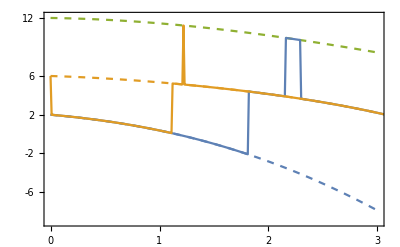

```mathematica
plotEV1={Plot[Interpolation[ImportCSV[spectralFiles[{#,1}]]][c]&/@{1,2,3}//Evaluate,{c,0,3.0},PlotStyle->Dashed,Frame->True],
ListPlot[ImportCSV[leaverFiles[{#,1}]]&/@{1,2},Joined->True,Frame->True,
PlotLegends->LineLegend[ColorData[97,#]&/@Range[3],TeX[{"1, 1","2, 1","3, 1"}],LegendLabel->TeX["\\ell, m"]]]}//
Show[#,PlotRange->{{0,3},Automatic},plotDirs,PlotRangePadding->{0,{0.5,1.5}},
FrameLabel->TeX[{"c","{}_{\\pm 1}\\mathscr{E}_{\\ell m}"}],
FrameTicks->{ticks@{-6,-2,2,6,12},ticks@Range[0,3,0.5]}
]&
Export[thesisPath<>"discontinuities",plotEV1]
```